## 1st Assignment: Stochastic FEM F. I. Giasemis

### A: KL expansion

#### Parameters from the problem

```mathematica
b=2;
a=2.5;
M=40; (* Number of terms in the KL expansion. *)
R=5000; (* Number of realizations. *)
```

#### Eigenvalues and eigenfunctions for f(x)

```mathematica
For[n=0,n<M,n=n+1;
If[OddQ[n], 
sol=NSolve[{1/b -x Tan[x a]==0,(n-1) Pi/a≤x≤(n-1/2) Pi/a},x];
w[n]=Part[x/.sol,1];
λ[n]=2b/(1+w[n]^2 b^2);
c[n]=1/Sqrt[a+Sin[2 w[n] a]/(2 w[n])];
φ[n][x_]:=c[n] Cos[w [n]x],
sol=NSolve[{1/b Tan[x a]+x==0,(n-1/2) Pi/a≤x≤(n) Pi/a},x];
w[n]=Part[x/.sol,1];
λ[n]=2b/(1+w[n]^2 b^2);
c[n]=1/Sqrt[a-Sin[2 w[n] a]/(2 w[n])];
φ[n][x_]:=c[n] Sin[w[n] x]
]
]
```

#### Random variables ξ(θ)

```mathematica
For[i=0,i<R,i=i+1;
ξ[i]=RandomVariate[NormalDistribution[],M]
]
```

#### Realization of f(x) and E(x)

```mathematica
RealizationF[i_,x_]:=Sum[Sqrt[λ[n]]φ[n][x-2.5]ξ[i][[n]],{n,1,M}];
Realization[i_,x_]:=10(1+RealizationF[i,x]);
```

#### Example plot of a realization of E(x)

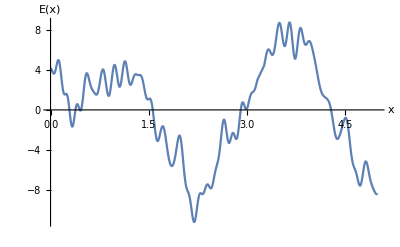

```mathematica
Plot[Realization[567,x],{x,0,5},AxesLabel->{"x","E(x)"}]
```

#### Ensemble averages and variances

```mathematica
EnsembleAverage[x_]:=Mean[Table[Realization[i,x],{i,1,R}]]
EnsembleVariance[x_]:=Variance[Table[Realization[i,x],{i,1,R}]]
```

#### Variance error

```mathematica
VarianceError[x_]:=10^2-10^2 Sum[λ[n]φ[n][x-2.5]^2,{n,1,M}]
```

#### Example calculation of ensemble average, variance and variance error

```mathematica
EnsembleAverage[2]
EnsembleVariance[2]
VarianceError[2]
```

10.0014

74.4098

23.155

#### Plot of 10 realizations

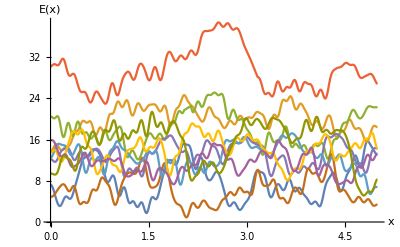

```mathematica
list={};
For[i=0,i<10,i=i+1;
AppendTo[list,Realization[i,x]]
]
Plot[list,{x,0,5},AxesLabel->{"x","E(x)"}]
```

#### Plot of 10 realizations

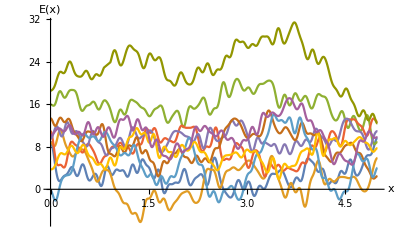

```mathematica
list={};
For[i=4300,i<4310,i=i+1;
AppendTo[list,Realization[i,x]]
]
Plot[list,{x,0,5},AxesLabel->{"x","E(x)"}]
```

#### Number of terms in the KL expansion

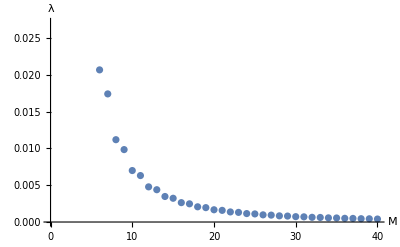

```mathematica
ListPlot[Table[λ[n],{n,1,M}],AxesLabel->{"M","λ"}]
```

```mathematica
λ[M]/λ[1]
```

0.000157685